Laboratory #6: Oscilloscopes and Circuits
J.R. Powers-Luhn
NE550, Thursday 17:30-20:30
Partner:
Station:

Pre-laboratory Questions

1. Read the laboratory assignment in its entirety before coming to lab.

Check

2. Read the Wikipedia page on oscilloscope (https://en.wikipedia.org/wiki/Oscilloscope).

Check

3. What is the purpose of AC coupling on an oscilloscope?

This presents on the the time-varying portions of the signal, without the DC voltage that this signal might be “riding” on.

4. What is the most common use of an oscilloscope?

According to Wikipedia (https://en.wikipedia.org/wiki/Oscilloscope#Examples_of_use), “[o]ne of the most frequent uses of scopes is troubleshooting malfunctioning electronic equipment.” Using the oscilloscope it is possible to probe in between components in a signal path, comparing the measured output against some expected result. In this way it is possible, via binary troubleshooting, to find the faulty component in 2^-n time, where n is the number of components.

5. In a DMM, the resistance values will change as a function of the current magnitude being measured. Explain why this happens and if this could affect a measured value in a given experiment.

The resistance value changes because the ammeter introduces a series resistor of known size and measures the voltage drop across that resistor in order to calculate current in the circuit. The resistor value is chosen to interfere only minimally with the circuit (i.e. the resistor in the DMM is small compared to the resistance of the circuit being measured), but it must also be sized to produce a measurable voltage drop across the measurement resistor. Because of this compromise, the different resistance values for each setting of the DMM may produce slightly different results.

6. In class we analytically solved the differential equation describing a CR network.
	a. Graphically display via plotting software how the input sinusoidal wave is modified at the output when modifying the input frequency. Plot the cases when the input frequency varies in decades from 10^3-10^7 Hz. Use a time constant of one microsecond, a peak-to-peak input amplitude of two volts, and a time domain covering at least four periods. Put the input and output on a single plot (5 plots total).

```mathematica
Clear[τ,Subscript[V, 0]]
```

Clear::ssym: V_0 is not a symbol or a string.

```mathematica
Subscript[V, in][f_, Subscript[V, 0]_, t_]:=Subscript[V, 0] Sin[2 π f t];
DSolve[{Subscript[V, 0] 2 π f * Cos[2 π f t]==V[t]/τ+V'[t],V[0]==0},V[t],t][[1,1,2]]
```

(2 ⅇ^(-t/τ) f π τ (-1+ⅇ^(t/τ) Cos[2 f π t]+2 ⅇ^(t/τ) f π τ Sin[2 f π t]))/(1+4 f^2 π^2 τ^2)

```mathematica
Subscript[V, out][f_,Subscript[V, 0]_,t_,τ_]:=(2 ⅇ^(-t/τ) f π τ (-1+ⅇ^(t/τ) Cos[2 f π t]+2 ⅇ^(t/τ) f π τ Sin[2 f π t]))/(1+4 f^2 π^2 τ^2)
```

```mathematica
tau=10*10^-6; (* seconds *)
Subscript[V, 0]=1; (* volts, corresponds to 2V peak-to-peak *)
```

Input frequency: 10^3 Hz:

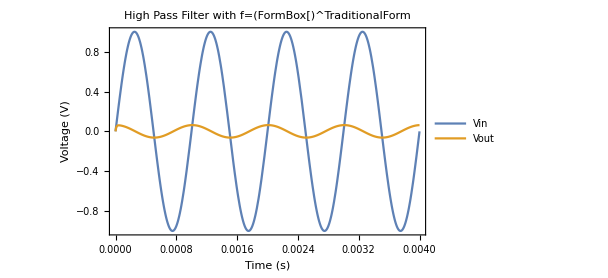

```mathematica
f=10^3;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

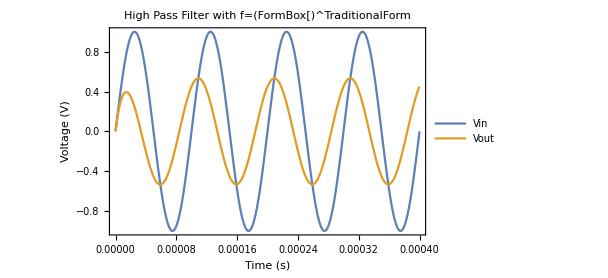

```mathematica
f=10^4;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

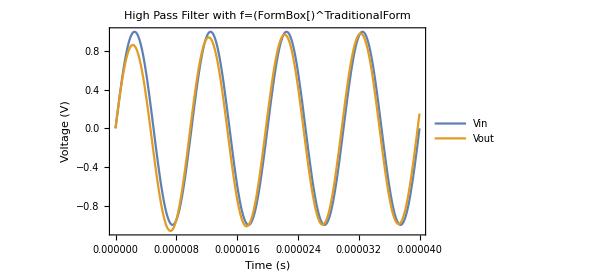

```mathematica
f=10^5;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

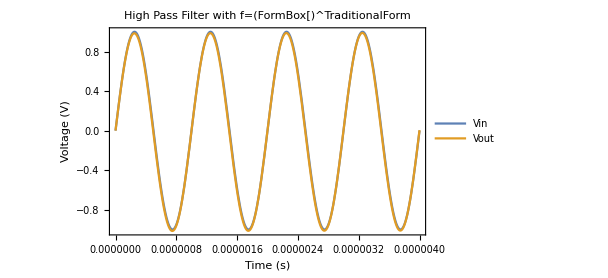

```mathematica
f=10^6;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

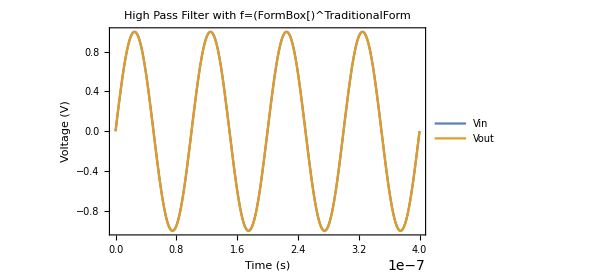

```mathematica
f=10^7;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

b. Determine the relative (fractional) attenuation of the amplitude as a function of the quotient of cutoff frequency to the input sine wave frequency (i.e. f_cutoff/f_sin). Do not forget to account for the 2π.

This attenuation is given in the text as equation 10.23, (V_(o,m))/(V_(i,m))=R/(√(R^2+1/(2 π f C)^2)). Since the cutoff frequency is given by f_0=1/(2 π R C), if we designate r=f_0/f, we arrive at  (V_(o,m))/(V_(i,m))=R/(√(R^2+(rR)^2))=R/(√(R^2(1+r^2)))=1/(√(1+r^2)).

c. Print out the Mathematica Notebook and turn in the solution with the rest of your prelab assignment.

Here you go!

## In-Lab

```mathematica
Import["/Users/jrpowers-luhn/nucnotes/ne550/Lab 6/LAB/DS0002.CSV"]
```

{{Memory Length,25000,},{Trigger Level,304mV,},{Source,CH1,},{Probe Ratio,1.,},{Vertical Units,V,},{Vertical Scale,0.2,},{Vertical Position,0.152,},{Horizontal Units,S,},{Horizontal Scale,0.0001,},{Horizontal Position,0.,},{Horizontal Mode,Main,},24994,{0.00049956,0.496,},{0.0004996,0.504,},{0.00049964,0.504,},{0.00049968,0.496,},{0.00049972,0.496,},{0.00049976,0.496,},{0.0004998,0.496,},{0.00049984,0.488,},{0.00049988,0.512,},{0.00049992,0.496,},{0.00049996,0.504,}}
 |  |  |  |

High Pass Filter

```mathematica
HighPassSquareWaveData=Multicolumn[Join[Import["/Users/jrpowers-luhn/nucnotes/ne550/Lab 6/LAB/DS0002.CSV"][[17;;]][[;;,1]],Import["/Users/jrpowers-luhn/nucnotes/ne550/Lab 6/LAB/DS0002.CSV"][[17;;]][[;;,2]]],2]//First
```

{{-0.0005,0.496},{-0.00049996,0.488},{-0.00049992,0.504},{-0.00049988,0.496},{-0.00049984,0.496},{-0.0004998,0.488},{-0.00049976,0.496},{-0.00049972,0.488},{-0.00049968,0.496},{-0.00049964,0.488},{-0.0004996,0.504},{-0.00049956,0.488},{-0.00049952,0.504},24974,{0.00049948,0.504},{0.00049952,0.496},{0.00049956,0.496},{0.0004996,0.504},{0.00049964,0.504},{0.00049968,0.496},{0.00049972,0.496},{0.00049976,0.496},{0.0004998,0.496},{0.00049984,0.488},{0.00049988,0.512},{0.00049992,0.496},{0.00049996,0.504}}
 |  |  |  |

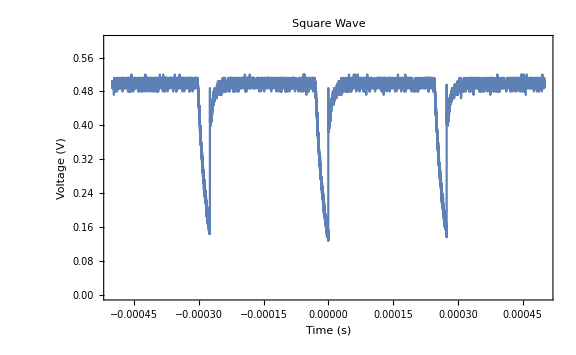

```mathematica
ListPlot[HighPassSquareWaveData,
Axes->True,
PlotRange->{{-0.0005,0.0005},{0,0.6}},
Joined->True,
Frame->True,
FrameLabel->{Style["Time (s)",Black,18],Style["Voltage (V)",Black,18]},
ImageSize->Large,
PlotLabel->Style["Square Wave",Black,24],
FrameTicksStyle->Directive[{Black,18},{Black,18}]
]
```